```mathematica
ClearAll["Global`*"];
fac = 1.0;

interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_aOff/fac_"<>ToString[NumberForm[fac,{1,1}]]<>"/sol.mx"];

uSolC = interpList[[1]];
vSolC[r_,t_]:=Evaluate[D[uSolC[r,tp],tp]/.tp->t];
uSolL = interpList[[2]];
vSolL[r_,t_]:=Evaluate[D[uSolL[r,tp],tp]/.tp->t];

(*domain values*)
rMin=0.1; (*μm*)
rMax=30; (*μm*)
tMax=250; (*s*)


release = 2*tMax; (* turn off pulsing *)
flat = 0.2; (* homogeneity after illuminated region *)
aOff = fac; (* degree of accumulation *)
n = 2; (* sharpness of accumulation *)
v = 1.0;

(*light activation values*)
width=1; (*μm,width of gaussian beam*)
r0=15; (*μm,radius of circle*)
cyc=1;
len=0.25; (*s*)
del=0.025; (*s*)

(*mechanical values*)
λ0=1.6;(*μm^2/s,1st Lame modulus slope*)
μ0=1.6; (*μm^2/s,2nd Lame modulus slope*)
gMin=0.4; (*shrinking factor of activated TCB2*)

(*import functions*)
Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2FunctionsND.m"]
```

```mathematica
Manipulate[Plot[{uSolC[r,t],uSolL[r,t]},{r,rMin,rMax},PlotRange->{-1,2}],{t,0,tMax}]
```

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

```mathematica
p= 60;
padding={{p,p/6},{p,p/6}};

Manipulate[Grid[{{Plot[CB[r,t],{r,rMin,rMax},ImageSize->500,PlotStyle->Black,PlotRange->{-0.01,1},FrameLabel->{None,"C_B"},
ImagePadding->padding]},
{Plot[{vSolC[r,t],vSolL[r,t]},{r,rMin,rMax},PlotRange->{-0.5,0.5},PlotStyle->{Directive[Blue],Directive[Red]},ImagePadding->padding,FrameLabel->{"r","v"},
PlotPoints->150,ImageSize->500]}}]
,{t,240,250,0.1}]
```

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

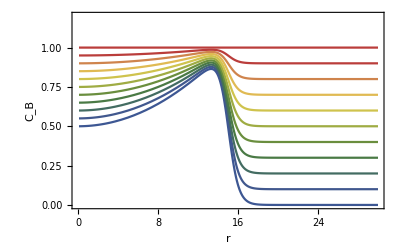

```mathematica
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];
Clear[r];
functions = Evaluate[Table[f[r,1,flat,0.5,2,0],{flat,0,1,0.1}]];

Plot[functions,{r,rMin,rMax},
PlotRange->{0,1.2},
FrameLabel->{"r","C_B"},
ImageSize->400,
PlotStyle->Table[ColorData["DarkRainbow", i/(Length[functions]-1)],{i,0,Length[functions]-1}]]
```

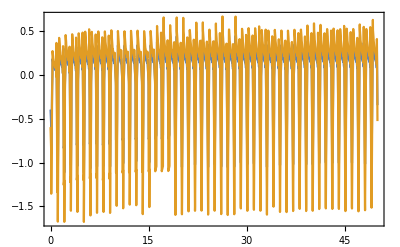

```mathematica
Plot[{vSolC[15,t],vSolL[15,t]},{t,0,50}]
```

```mathematica
Manipulate[Plot[iFun[t],{t,0,3},PlotPoints->100,Epilog->{Line[{{tt,0},{tt,1}}]}],{tt,0,2}]
```

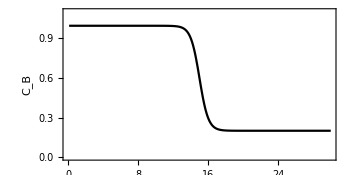
-Graphics- | 
-Graphics- |

```mathematica
SetOptions[DensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

rC = 0.5;
ul = rC;
ll = -rC;
tup=250;
tl = tup-5;
tu = tup;

cf=ColorData["ThermometerColors"][(#-ll)/(ul-ll)]&;

scaleFunc[x_,a_,w_]:=a Tanh[x/w];

p= 60;
padding={{p,p/6},{p,p/6}};
paddingIns={{p,p/6},{p/2,p/6}};

size = 350;

pIns = Plot[CB[r,1+len/2],{r,rMin,rMax},PlotStyle->Black,
PlotRange->{0,1.1},FrameLabel->{None,"C_B"},
FrameTicks->Automatic,
ImageSize->size,
AspectRatio->1/2, 
ImagePadding->paddingIns];

legend = BarLegend[{cf,{ll,ul}},LegendLabel->"v(r,t)",
LabelStyle->{FontFamily->"Arial",Black,FontSize->16},
LegendMarkerSize->400(*, ColorFunctionScaling->True*)];

pF=Show[
DensityPlot[scaleFunc[vSolC[r,t],rC,0.3],{r,rMin,rMax},{t,tl,tu}, 
PlotRange->{ll,ul},
PlotPoints->200,
AspectRatio->2,
ImageSize->size,
Axes->False,
ColorFunction->cf,
ColorFunctionScaling->False,
FrameLabel->{"r","Time"},
ImagePadding->padding
],

ParametricPlot[{7*iFun[t],t},{t,tl,tu},PlotPoints->200,PlotRange->{tl,tu},PlotStyle->Directive[Black,Thick]]
];
pCom=Grid[{{pIns,""},{pF,legend}}]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Figures/aOff1Scaled.jpg",pCom,ImageResolution->400];
```

```mathematica
zetaC[tu_,tl_,ru_,rl_]:=(NIntegrate[vSolC[r,t]*gamFunc[r,t]*r,{r,rMin,rMax},{t,tl,tu}, WorkingPrecision->8,Method->{"GlobalAdaptive","MaxErrorIncreases"->2000,Method->"GaussKronrodRule"},MaxRecursion->10] /((tu-tl)*(rMax-rMin)))

zetaL[tu_,tl_,ru_,rl_]:=(NIntegrate[vSolL[r,t]*gamFunc[r,t],{r,rMin,rMax},{t,tl,tu}, WorkingPrecision->8,Method->{"GlobalAdaptive","MaxErrorIncreases"->2000,Method->"GaussKronrodRule"},MaxRecursion->10] /((tu-tl)*(rMax-rMin)))
```

```mathematica
facList = {0.0, 0.1, 0.2, 0.3, 0.4, 0.5,0.6, 0.7, 0.8, 0.9, 1.0};
zetaLList = {};
zetaCList = {};

tl = 240;
tu = 250;
Do[
fac = facList[[i]];
interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_v/fac_"<>ToString[NumberForm[fac,{1,1}]]<>"/sol.mx"];
vSolC[r_,t_]:=Evaluate[D[uSolC[r,tp],tp]/.tp->t];

uSolC = interpList[[1]];
vSolC[r_,t_]:=Evaluate[D[uSolC[r,tp],tp]/.tp->t];
uSolL = interpList[[2]];
  vSolL[r_,t_]:=Evaluate[D[uSolL[r,tp],tp]/.tp->t];

zetaCV = zetaC[tl,tu,rMin,rMax];
AppendTo[zetaCList, zetaCV];

zetaLV = zetaL[tl,tu,rMin,rMax];
AppendTo[zetaLList, zetaLV];

Print[i];

,{i,1,Length[facList]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2

3

4

5

6

7

8

9

10

11

```mathematica
(*dataL = Transpose[{facList,zetaLList}];
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_v/zetaListT10_L.mat",dataL];

dataC = Transpose[{facList,zetaCList}];
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_v/zetaListT10_C.mat",dataC];*)
```

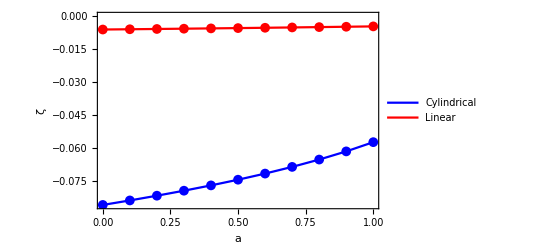

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];


var = "v";
dataC = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_"<>var<>"/zetaListT10_C.mat","Data"][[1]];
dataL = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_ND/Dirs_"<>var<>"/zetaListT10_L.mat","Data"][[1]];

ps = 7;

pD=Show[
ListPlot[{dataC,dataL},Joined->True, PlotStyle->{Directive[Blue],Directive[Red]},
FrameLabel->{"a","ζ"},ImageSize->400, PlotLegends->Placed[{"Cylindrical","Linear"},{0.8,0.2}]],
ListPlot[{dataC,dataL},PlotStyle->{Directive[Blue,AbsolutePointSize[ps]],Directive[Red,AbsolutePointSize[ps]]}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Figures/gMinzeta.jpg",pD,ImageResolution->400];
```

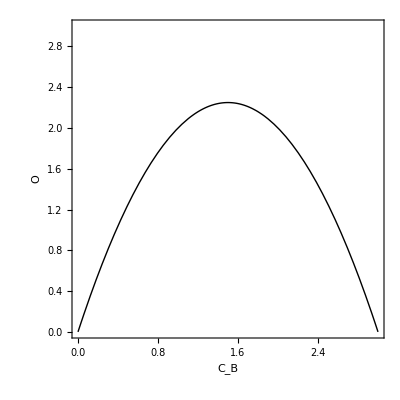

```mathematica
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];


Cs = 3;
Plot[Cs^2/4-(x-Cs/2)^2,{x,0,Cs},PlotRange->{0,Cs},AspectRatio->1,Frame->True,PlotStyle->{Black,Thick},FrameLabel->{"C_B","O"},FrameStyle->Black]
```